```mathematica
(*==================================================================================*)
(*-------------------------Hamamatsu measure the air, light on--------------------------*)
(*==================================================================================*)
```

```mathematica
filePath = SystemDialogInput["FileOpen"]
```

G:\FTIR\near infrared machine examination\Hamamatsu FTIR engine test\gain1 light on\Spectrum.csv

```mathematica
SystemOpen[filePath]
wn = Import[filePath,{"Data",All,3}];
```

```mathematica
logicList =(NumericQ[#])&/@lighton ;(*Find elements not a numeric*)
```

```mathematica
dropIndex = Flatten@Position[logicList,False];
```

```mathematica
wnlighton = Drop[lighton,{1,Max@dropIndex}];
```

```mathematica
(*the 4th column values*)
```

```mathematica
lighton = Import[filePath,{"Data",All,4}];
```

```mathematica
effectlight = (NumericQ[#])&/@lighton;
```

```mathematica
dropIndex1 = Flatten@Position[effectlight,False];
```

```mathematica
valLightOn = Drop[lighton,{1,Max@dropIndex1}];
```

```mathematica
lightOnSampleSet = Transpose@Append[{wnlighton},valLightOn];
```

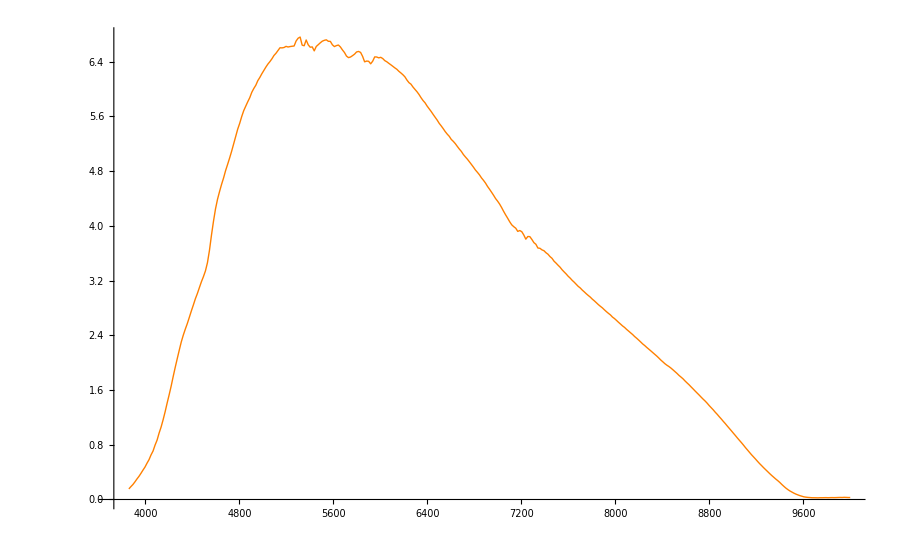

```mathematica
ListPlot[lightOnSampleSet,PlotRange->All,Joined->True,PlotStyle->{Thin,Orange}]
```

```mathematica
(*==================================================================================*)
(*-------------------------Hamamatsu measure the air, light off--------------------------*)
(*==================================================================================*)
```

```mathematica
filePath1 = SystemDialogInput["FileOpen"]
```

G:\FTIR\near infrared machine examination\Hamamatsu FTIR engine test\gain1 light off\Spectrum.csv

```mathematica
SystemOpen[filePath1]
wn1 = Import[filePath1,{"Data",All,3}];
```

```mathematica
effectWN =(NumericQ[#])&/@wn1 ;(*Find elements not a numeric*)
```

```mathematica
dropIndex2 = Flatten@Position[effectWN,False];
```

```mathematica
wavelengthLightOff = Drop[wn1,{1,Max@dropIndex2}];
```

```mathematica
wnLightOff=10^7/wavelengthLightOff;
```

```mathematica
lightOff = Import[filePath1,{"Data",All,4}];
```

```mathematica
effectlightOff = (NumericQ[#])&/@lightOff;
```

```mathematica
dropIndex3 = Flatten@Position[effectlightOff,False];
```

```mathematica
valLightOff = Drop[lightOff,{1,Max@dropIndex3}];
```

```mathematica
Clear@lightOffSampleSet
```

```mathematica
lightOffSampleSet = Transpose@Append[{wnLightOff},valLightOff];
```

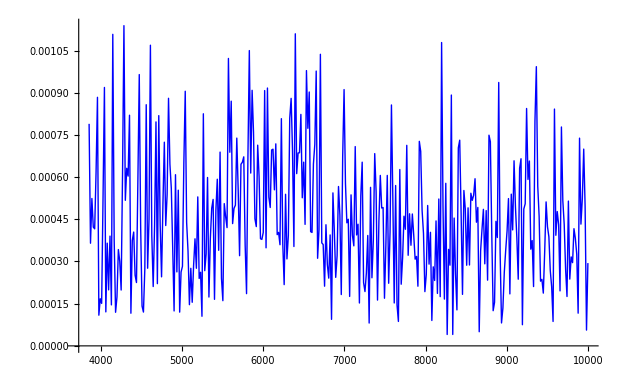

```mathematica
ListPlot[lightOffSampleSet,PlotRange->All,Joined->True,PlotStyle->{Thin,Blue}]
```

```mathematica
(*==================================================================================*)
(*--------------------------------------SNR value------------------------------------*)
(*==================================================================================*)
```

```mathematica
snr = Max@valLightOn/StandardDeviation[valLightOff]
```

28795.5

```mathematica
(*==================================================================================*)
(*--------------------------西派特 measure the air, light on---------------------------*)
(*----------------------------------- 2022-3-10-------------------------------------*)
(*==================================================================================*)
```

```mathematica
filePath2 = SystemDialogInput["FileOpen"]
```

G:\FTIR\near infrared machine examination\西派克2022.03.10 信号噪声 测试\信号测试\信号 - 03-10 09-41-36_C_2.txt

```mathematica
SystemOpen[filePath2]
西派特 = Import[filePath2,"Data"];
```

```mathematica
Clear@filePath2
```

```mathematica
Clear@西派特
```

```mathematica
西派特wavelength =西派特⟦All,1⟧;
```

```mathematica
西派特val = 西派特⟦All,2⟧;
```

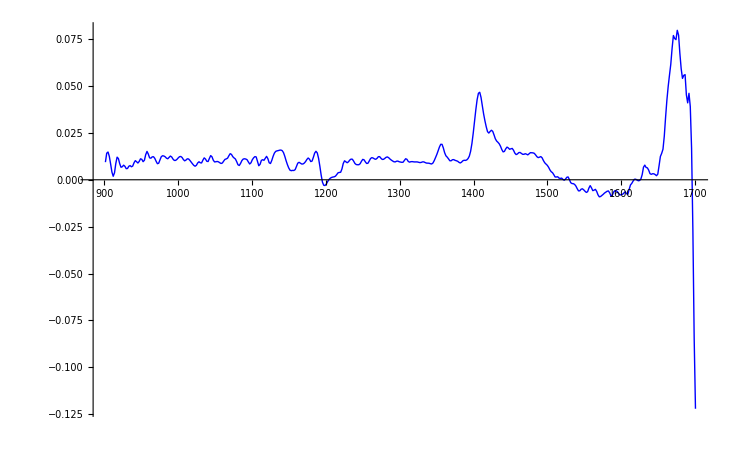

```mathematica
ListPlot[西派特, PlotRange->All,Joined->True,PlotStyle->{Thin,Blue}]
```

```mathematica
(*==================================================================================*)
(*---------------------------Hamamatsu test, 1% methyl alcohol--------------------------*)
(*==================================================================================*)
```

```mathematica
Hama1per = SystemDialogInput["FileOpen"]
```

G:\FTIR\near infrared machine examination\Hamamatsu FTIR engine test\1% 甲醇汽油3\Absorbance.csv

```mathematica
Clear@Hama1perWN
```

```mathematica
Clear@Hama1perSet
```

```mathematica
SystemOpen[Hama1per]
Hama1perWNraw = Import[Hama1per,{"Data",All,1}];
```

```mathematica
effectHama1perWN = (NumericQ[#])&/@Hama1perWNraw;
```

```mathematica
dropIndexHama1per = Flatten@Position[effectHama1perWN,False];
```

```mathematica
Hama1perWN = Drop[Hama1perWNraw,{1,Max@dropIndexHama1per}];
```

```mathematica
Hama1perVal = Import[Hama1per,{"Data",All,3}];
```

```mathematica
Hama1perValNew = Drop[Hama1perVal,{1,Max@dropIndexHama1per}];
```

```mathematica
Hama1perSet = Transpose@Append[{Hama1perWN},Hama1perValNew]
```

{{3859.04,0.94773},{3876.19,0.881674},{3893.34,0.908023},{3910.49,1.01288},{3927.64,1.06307},{3944.79,1.18087},{3961.94,1.44369},{3979.09,1.613},{3996.25,2.14642},{4013.4,1.88971},{4030.55,1.77493},{4047.7,1.70658},{4064.85,1.64163},{4082.,1.83389},{4099.15,2.12548},{4116.31,2.35947},{4133.46,2.48296},{4150.61,2.1946},{4167.76,2.38839},{4184.91,2.37464},{4202.06,2.42199},{4219.21,2.49942},{4236.36,2.61675},{4253.52,2.33418},{4270.67,2.17835},{4287.82,2.29971},{4304.97,2.25571},{4322.12,2.16536},{4339.27,2.30142},{4356.42,2.26134},{4373.57,2.1914},{4390.73,2.40841},{4407.88,2.31954},{4425.03,2.24562},{4442.18,2.48982},{4459.33,2.34003},{4476.48,2.01671},{4493.63,1.82885},{4510.78,1.66392},{4527.94,1.51201},{4545.09,1.53554},{4562.24,1.68936},{4579.39,1.89731},{4596.54,2.2102},{4613.69,2.66474},{4630.84,1.94551},{4647.99,1.67744},{4665.15,1.70588},{4682.3,1.25692},{4699.45,0.860638},{4716.6,0.727247},{4733.75,0.677918},{4750.9,0.633852},{4768.05,0.617522},{4785.2,0.614433},{4802.36,0.595055},{4819.51,0.58915},{4836.66,0.593378},{4853.81,0.603272},{4870.96,0.621447},{4888.11,0.645839},{4905.26,0.661178},{4922.41,0.668914},{4939.57,0.690841},{4956.72,0.689294},{4973.87,0.675129},{4991.02,0.649883},{5008.17,0.623869},{5025.32,0.598683},{5042.47,0.585374},{5059.63,0.571654},{5076.78,0.566843},{5093.93,0.566803},{5111.08,0.55243},{5128.23,0.542433},{5145.38,0.547383},{5162.53,0.551457},{5179.68,0.550224},{5196.84,0.557689},{5213.99,0.566798},{5231.14,0.567005},{5248.29,0.569934},{5265.44,0.572024},{5282.59,0.573897},{5299.74,0.59232},{5316.89,0.617423},{5334.05,0.623164},{5351.2,0.609677},{5368.35,0.602136},{5385.5,0.61713},{5402.65,0.661295},{5419.8,0.724917},{5436.95,0.797776},{5454.1,0.857112},{5471.26,0.894773},{5488.41,0.902099},{5505.56,0.883757},{5522.71,0.847329},{5539.86,0.844112},{5557.01,0.886404},{5574.16,0.943988},{5591.31,1.02697},{5608.47,1.20381},{5625.62,1.57525},{5642.77,2.08844},{5659.92,2.30813},{5677.07,2.23266},{5694.22,2.23037},{5711.37,2.39197},{5728.52,2.73411},{5745.68,2.78467},{5762.83,2.68795},{5779.98,2.54949},{5797.13,2.39522},{5814.28,2.28845},{5831.43,2.20504},{5848.58,2.07274},{5865.73,1.97201},{5882.89,1.9157},{5900.04,1.8458},{5917.19,1.82311},{5934.34,1.89454},{5951.49,2.08886},{5968.64,1.88765},{5985.79,1.29298},{6002.94,0.874802},{6020.1,0.59883},{6037.25,0.426461},{6054.4,0.343587},{6071.55,0.329271},{6088.7,0.326872},{6105.85,0.303318},{6123.,0.279868},{6140.16,0.231038},{6157.31,0.179221},{6174.46,0.135642},{6191.61,0.109127},{6208.76,0.0918526},{6225.91,0.0784409},{6243.06,0.069351},{6260.21,0.0631674},{6277.37,0.058518},{6294.52,0.0550745},{6311.67,0.0523397},{6328.82,0.0485581},{6345.97,0.0456196},{6363.12,0.0438117},{6380.27,0.0425791},{6397.42,0.0417993},{6414.58,0.0418866},{6431.73,0.0423544},{6448.88,0.0423679},{6466.03,0.0427887},{6483.18,0.0437742},{6500.33,0.0448375},{6517.48,0.046331},{6534.63,0.0486819},{6551.79,0.0525358},{6568.94,0.0569846},{6586.09,0.0621982},{6603.24,0.0693345},{6620.39,0.0769108},{6637.54,0.0871025},{6654.69,0.101282},{6671.84,0.115645},{6689.,0.124292},{6706.15,0.130715},{6723.3,0.136187},{6740.45,0.142765},{6757.6,0.150046},{6774.75,0.16083},{6791.9,0.170821},{6809.05,0.173234},{6826.21,0.172318},{6843.36,0.173532},{6860.51,0.177282},{6877.66,0.190068},{6894.81,0.21122},{6911.96,0.231351},{6929.11,0.243956},{6946.26,0.261343},{6963.42,0.286373},{6980.57,0.300189},{6997.72,0.294425},{7014.87,0.28892},{7032.02,0.30074},{7049.17,0.339455},{7066.32,0.401401},{7083.48,0.442984},{7100.63,0.443769},{7117.78,0.451848},{7134.93,0.474906},{7152.08,0.487393},{7169.23,0.521405},{7186.38,0.536956},{7203.53,0.503462},{7220.69,0.477824},{7237.84,0.477296},{7254.99,0.461382},{7272.14,0.407334},{7289.29,0.35098},{7306.44,0.301633},{7323.59,0.271863},{7340.74,0.261631},{7357.9,0.229628},{7375.05,0.159256},{7392.2,0.095169},{7409.35,0.057461},{7426.5,0.0371342},{7443.65,0.0249547},{7460.8,0.0174884},{7477.95,0.0123389},{7495.11,0.00844606},{7512.26,0.00611194},{7529.41,0.00462577},{7546.56,0.00344875},{7563.71,0.00363815},{7580.86,0.00369983},{7598.01,0.00418077},{7615.16,0.00514041},{7632.32,0.00623557},{7649.47,0.00729782},{7666.62,0.00792273},{7683.77,0.00845483},{7700.92,0.00798639},{7718.07,0.00745011},{7735.22,0.00670522},{7752.37,0.00579574},{7769.53,0.00551407},{7786.68,0.00537601},{7803.83,0.00600647},{7820.98,0.00730351},{7838.13,0.00931439},{7855.28,0.0117918},{7872.43,0.0147744},{7889.58,0.0180309},{7906.74,0.0221006},{7923.89,0.0262128},{7941.04,0.0305835},{7958.19,0.0347884},{7975.34,0.0405253},{7992.49,0.045318},{8009.64,0.0501733},{8026.79,0.0561997},{8043.95,0.0640182},{8061.1,0.0733082},{8078.25,0.0845575},{8095.4,0.0979367},{8112.55,0.114638},{8129.7,0.134944},{8146.85,0.158603},{8164.01,0.183877},{8181.16,0.209628},{8198.31,0.237912},{8215.46,0.268131},{8232.61,0.295944},{8249.76,0.323526},{8266.91,0.352192},{8284.06,0.37366},{8301.22,0.387615},{8318.37,0.416576},{8335.52,0.471047},{8352.67,0.537874},{8369.82,0.606496},{8386.97,0.654726},{8404.12,0.657162},{8421.27,0.618962},{8438.43,0.543442},{8455.58,0.451623},{8472.73,0.376983},{8489.88,0.335685},{8507.03,0.308643},{8524.18,0.279435},{8541.33,0.252663},{8558.48,0.23138},{8575.64,0.212572},{8592.79,0.19302},{8609.94,0.174751},{8627.09,0.165951},{8644.24,0.17346},{8661.39,0.194109},{8678.54,0.217155},{8695.69,0.231501},{8712.85,0.222864},{8730.,0.199897},{8747.15,0.180182},{8764.3,0.159682},{8781.45,0.130772},{8798.6,0.0988075},{8815.75,0.0711925},{8832.9,0.0495107},{8850.06,0.0349688},{8867.21,0.0238473},{8884.36,0.0149277},{8901.51,0.00790133},{8918.66,0.00264485},{8935.81,-0.00166775},{8952.96,-0.00525517},{8970.11,-0.00744564},{8987.27,-0.00929206},{9004.42,-0.0106974},{9021.57,-0.0122424},{9038.72,-0.0126442},{9055.87,-0.0129757},{9073.02,-0.0133693},{9090.17,-0.0134177},{9107.33,-0.0137019},{9124.48,-0.0128408},{9141.63,-0.0113344},{9158.78,-0.011056},{9175.93,-0.00942873},{9193.08,-0.00784328},{9210.23,-0.00703336},{9227.38,-0.0057844},{9244.54,-0.00610525},{9261.69,-0.00646181},{9278.84,-0.00697556},{9295.99,-0.00665604},{9313.14,-0.00815791},{9330.29,-0.00860951},{9347.44,-0.00830379},{9364.59,-0.00914007},{9381.75,-0.00751557},{9398.9,-0.00730703},{9416.05,-0.00811351},{9433.2,-0.00823041},{9450.35,-0.0109297},{9467.5,-0.0176193},{9484.65,-0.0161053},{9501.8,-0.0215186},{9518.96,-0.0429237},{9536.11,-0.0524963},{9553.26,-0.0860798},{9570.41,-0.121289},{9587.56,-0.143144},{9604.71,-0.147017},{9621.86,-0.159598},{9639.01,-0.0993833},{9656.17,-0.0703254},{9673.32,-0.000410735},{9690.47,0.0545584},{9707.62,0.0635557},{9724.77,0.102352},{9741.92,0.180131},{9759.07,0.291722},{9776.22,0.425107},{9793.38,0.612846},{9810.53,0.511759},{9827.68,0.440811},{9844.83,0.347239},{9861.98,0.311998},{9879.13,0.381005},{9896.28,0.409805},{9913.43,0.506516},{9930.59,0.733383},{9947.74,1.20541},{9964.89,1.17412},{9982.04,0.637752},{9999.19,0.481905}}

```mathematica
peaks =FindPeaks[Hama1perSet⟦All,2⟧,1.5,0,0.5];
```

```mathematica
peakPos =Hama1perWN⟦peaks⟦;;,1⟧⟧;
```

```mathematica
Clear@peaksSet
```

```mathematica
peaksSet = Transpose[Append[{peakPos},peaks⟦All,2⟧]];
```

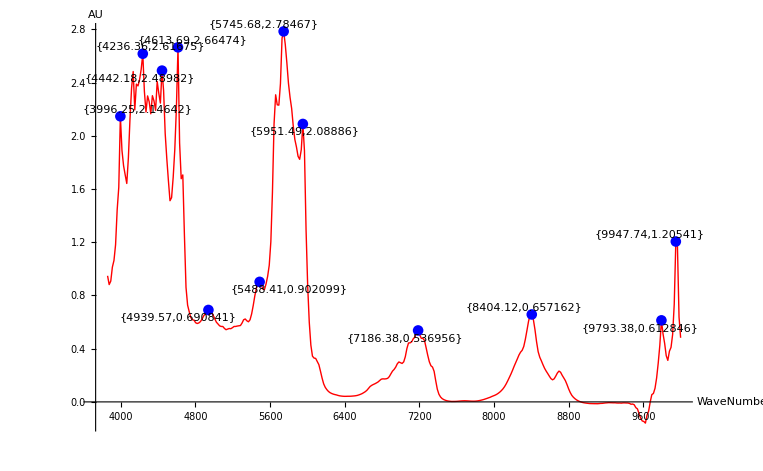

```mathematica
ListPlot[{Hama1perSet,Labeled[peaksSet,peaksSet,peaksSet]},PlotRange->All,Joined->{True,False},PlotStyle->{{Thin,Red},{PointSize[0.01],Blue}},AxesLabel->{"WaveNumber","AU"}]
```

```mathematica
(*==================================================================================*)
(*---------------------------西派特 test, 1% methyl alcohol--------------------------*)
(*==================================================================================*)
```

```mathematica
西派特1per = SystemDialogInput["FileOpen"]
```

G:\FTIR\near infrared machine examination\西帕克 FTIR测试\1% 甲醇汽油\甲醇汽油 - 03-08 21-28-00_C_1.txt

```mathematica
SystemOpen[Hama1per]
西派特1perWNraw = Import[西派特1per,"Data"];
```

```mathematica
西派特1per波长 =西派特1perWNraw⟦All,1⟧;
```

```mathematica
西派特1per波数 = 10^7/西派特1per波长;
```

```mathematica
西派特1per光谱 =西派特1perWNraw⟦All,2⟧;
```

```mathematica
西派特1per数集 =Transpose@Append[{西派特1per波数},西派特1per光谱];
```

```mathematica
西派特1per峰值 = FindPeaks[西派特1per光谱,0,0,0.2]
```

{{166,0.237487},{279,0.203956},{455,1.3433}}

```mathematica
西派特1per峰值位置 =西派特1per波数⟦西派特1per峰值⟦;;,1⟧⟧;
```

```mathematica
西派特1per峰值数集 = Transpose@Append[{西派特1per峰值位置},西派特1per峰值⟦All,2⟧];
```

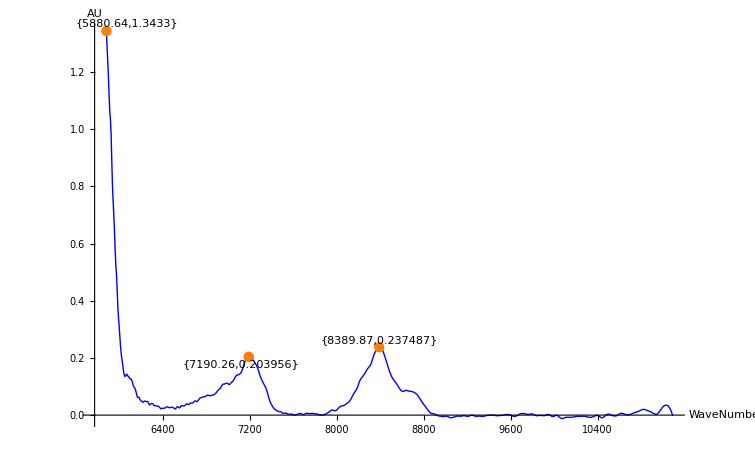

```mathematica
ListPlot[{西派特1per数集,Labeled[西派特1per峰值数集,西派特1per峰值数集,西派特1per峰值数集]},PlotRange->All,Joined->{True,False},PlotStyle->{{Thin,Blue},{PointSize[0.01],Orange}},AxesLabel->{"WaveNumber","AU"}]
```

```mathematica
8389.87-7190.26
```

1199.61

```mathematica
8404.12-7186.38
```

1217.74

```mathematica
8404.12-7186.38
```

```mathematica
(*==================================================================================*)
(*---------------------------Hamamatsu test, 13% methyl alcohol--------------------------*)
(*==================================================================================*)
```

```mathematica
Hama13per = SystemDialogInput["FileOpen"]
```

G:\FTIR\near infrared machine examination\Hamamatsu FTIR engine test\13% 甲醇汽油\Absorbance.csv

```mathematica
SystemOpen[Hama1per]
Hama13perRaw = Import[Hama13per,{"Data",All,1}];
```

```mathematica
effectHama13perWN = (NumericQ[#])&/@Hama13perRaw;
```

```mathematica
dropIndexHama13per = Flatten@Position[effectHama13perWN,False];
```

```mathematica
Hama13perWN = Drop[Hama13perRaw,{1,Max@dropIndexHama13per}];
```

```mathematica
Hama13perVal = Import[Hama13per,{"Data",All,3}];
```

```mathematica
Hama13perValNew = Drop[Hama13perVal,{1,Max@dropIndexHama13per}];
```

```mathematica
Hama13perSet = Transpose@Append[{Hama13perWN},Hama13perValNew];
```

```mathematica
peaks13 =FindPeaks[Hama13perSet⟦All,2⟧,1.5,0,0.5];
```

```mathematica
peakPos13 =Hama13perWN⟦peaks13⟦;;,1⟧⟧;
```

```mathematica
peaksSet13 = Transpose[Append[{peakPos13},peaks13⟦All,2⟧]];
```

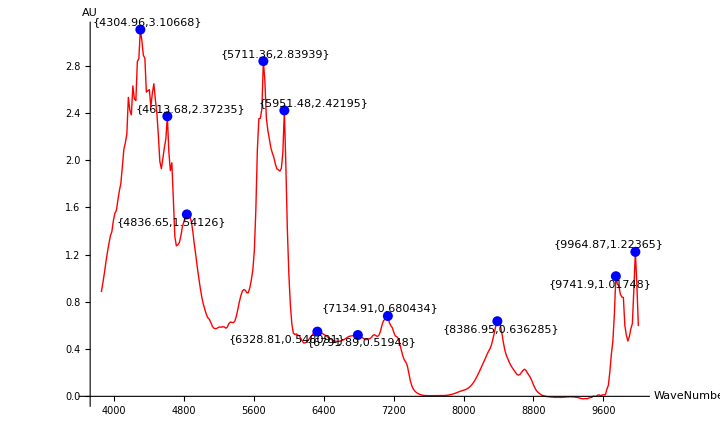

```mathematica
ListPlot[{Hama13perSet,Labeled[peaksSet13,peaksSet13,peaksSet13]},PlotRange->All,Joined->{True,False},PlotStyle->{{Thin,Red},{PointSize[0.01],Blue}},AxesLabel->{"WaveNumber","AU"}]
```

```mathematica
(*==================================================================================*)
(*---------------------------西派特 test, 13% methyl alcohol--------------------------*)
(*mathematica 做一个函数，可以通用的,module怎么返回值,如果不加冒号*)
(*==================================================================================*)
```

```mathematica
Xipaite[σ_,s_,t_]:=Module[{filepath,data,wavelength,waveNumber,spectrum,sampleSet,peaks,peakPos,peakSet},filepath = SystemDialogInput["FileOpen"];
                                                                       SystemOpen[filepath];
                                                                       data = Import[filepath,"Data"];
                                                                        wavelength=data⟦All,1⟧;
                                                                        waveNumber = 10^7/wavelength;
                                                                       spectrum = data⟦All,2⟧;
							      sampleSet = Transpose@Append[{waveNumber},spectrum];
  peaks =FindPeaks[sampleSet⟦All,2⟧,σ,s,t];
                                                                      peakPos =waveNumber⟦peaks⟦;;,1⟧⟧;
                                                                        peakSet = Transpose[Append[{peakPos},peaks⟦All,2⟧]];
ListPlot[{sampleSet,Labeled[peakSet,peakSet,peakSet]},PlotRange->All,Joined->{True,False},PlotStyle->{{Thin,Red},{PointSize[0.01],Blue}},AxesLabel->{"WaveNumber","AU"}]
];
```

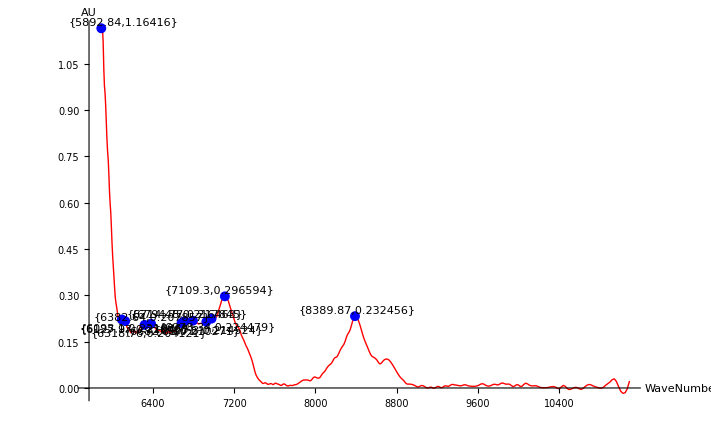

```mathematica
西派特13per =Xipaite[0.5,0,0.2]
```

```mathematica
Hamamatsu[σ_,s_,t_]:=Module[{filepath,WNRaw,filterData,dropIndex,waveNumber,valRaw,value,sampleSet,peaks,peakPos,peakSet},filepath = SystemDialogInput["FileOpen"];
                                                                       SystemOpen[filepath];
                                                                       WNRaw = Import[filepath,{"Data",All,1}];
                                                                       filterData = (NumericQ[#])&/@WNRaw;
                                                                       dropIndex = Flatten@Position[filterData,False];
                                                                       waveNumber = Drop[WNRaw,{1,Max@dropIndex}];
                                                                       valRaw = Import[filepath,{"Data",All,3}];
                                                                        value = Drop[valRaw,{1,Max@dropIndex}];
                                                                        sampleSet = Transpose@Append[{waveNumber},value];
                                                                        peaks =FindPeaks[sampleSet⟦All,2⟧,σ,s,t];
                                                                      peakPos =waveNumber⟦peaks⟦;;,1⟧⟧;
                                                                        peakSet = Transpose[Append[{peakPos},peaks⟦All,2⟧]];
ListPlot[{sampleSet,Labeled[peakSet,peakSet,peakSet]},PlotRange->All,Joined->{True,False},PlotStyle->{{Thin,Red},{PointSize[0.01],Blue}},AxesLabel->{"WaveNumber","AU"}]];
```

```mathematica
(*==================================================================================*)
(*---------------------------Hamamatsu test, 20% methyl alcohol--------------------------*)
(*mathematica 做一个函数，可以通用的,module怎么返回值,如果不加冒号*)
(*==================================================================================*)
```

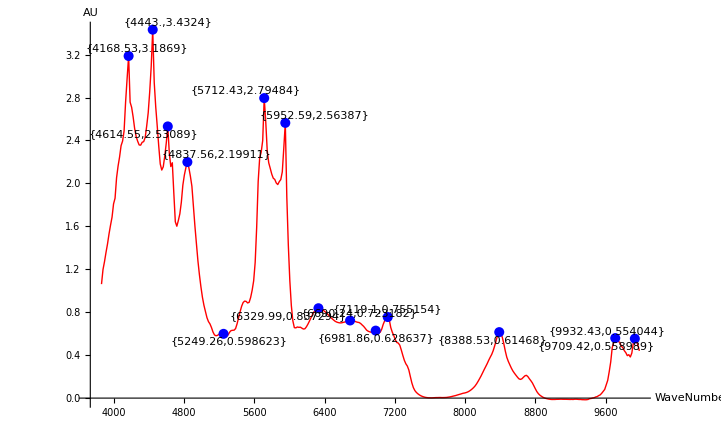

```mathematica
hamamatsu20per = Hamamatsu[1.5,0,0.5]
```

```mathematica
(*==================================================================================*)
(*---------------------------西派特 test, 20% methyl alcohol--------------------------*)
(*mathematica 做一个函数，可以通用的,module怎么返回值,如果不加冒号*)
(*==================================================================================*)
```

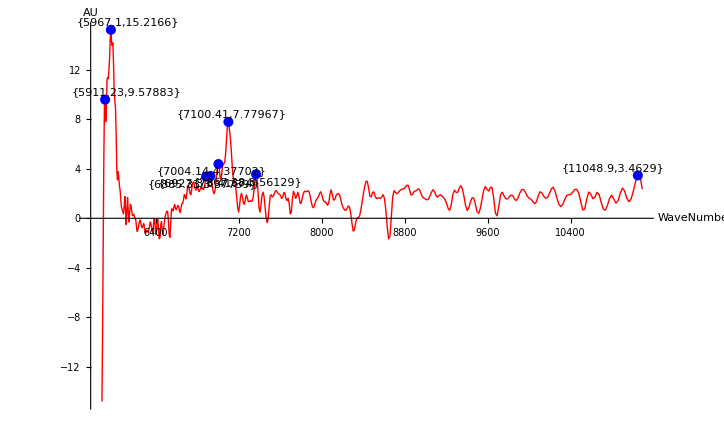

```mathematica
西派特20per =Xipaite[1,0,3]
```

```mathematica
(*==================================================================================*)
(*---------------------------Hamamatsu test, 24% methyl alcohol--------------------------*)
(*mathematica 做一个函数，可以通用的,module怎么返回值,如果不加冒号*)
(*==================================================================================*)
```

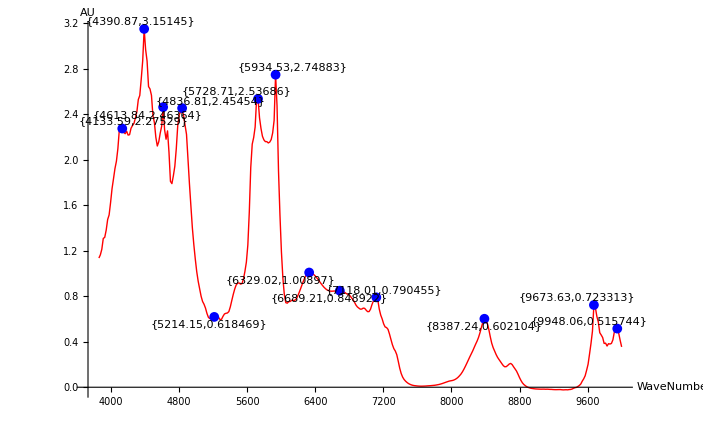

```mathematica
hamamatsu24per = Hamamatsu[1.5,0,0.5]
```

```mathematica
(*==================================================================================*)
(*---------------------------西派特 test, 24% methyl alcohol--------------------------*)
(*mathematica 做一个函数，可以通用的,module怎么返回值,如果不加冒号*)
(*==================================================================================*)
```

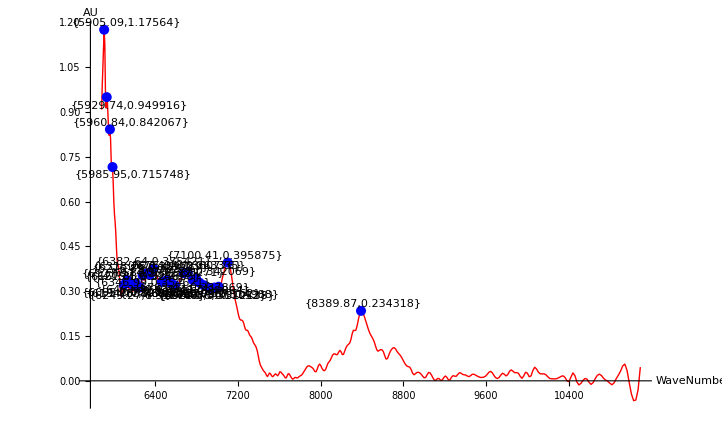

```mathematica
西派特24per =Xipaite[0,0,0.2]
```

```mathematica
(*==================================================================================*)
(*---------------------------Hamamatsu test, 29% methyl alcohol--------------------------*)
(*mathematica 做一个函数，可以通用的,module怎么返回值,如果不加冒号*)
(*==================================================================================*)
```

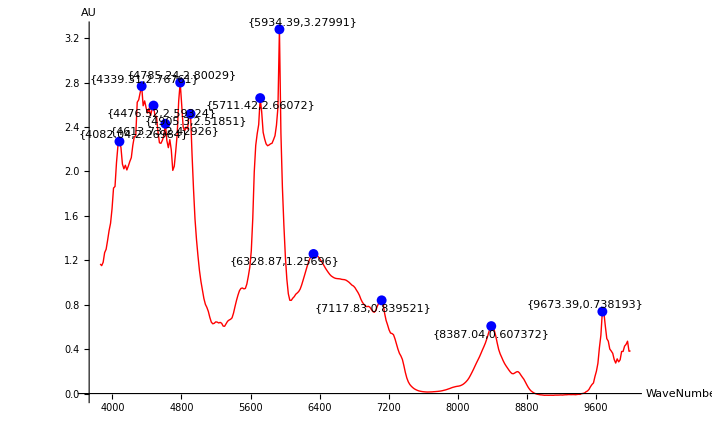

```mathematica
hamamatsu29per = Hamamatsu[1.5,0,0.5]
```

```mathematica
(*==================================================================================*)
(*---------------------------西派特 test, 29% methyl alcohol--------------------------*)
(*mathematica 做一个函数，可以通用的,module怎么返回值,如果不加冒号*)
(*==================================================================================*)
```

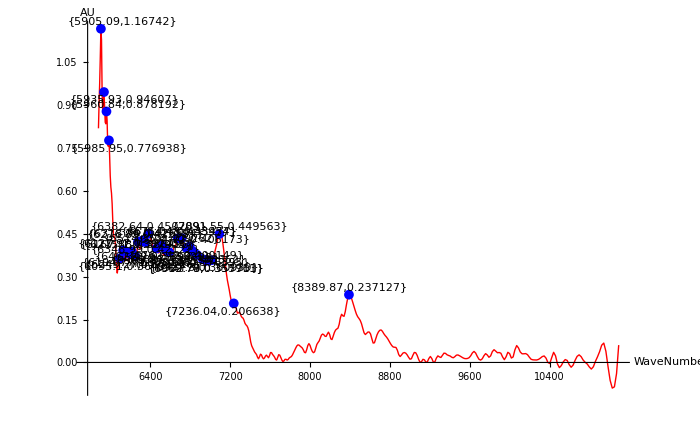

```mathematica
西派特29per =Xipaite[0,0,0.2]
```

```mathematica
(*==================================================================================*)
(*---------------------------Hamamatsu test, 35% methyl alcohol--------------------------*)
(*mathematica 做一个函数，可以通用的,module怎么返回值,如果不加冒号*)
(*==================================================================================*)
```

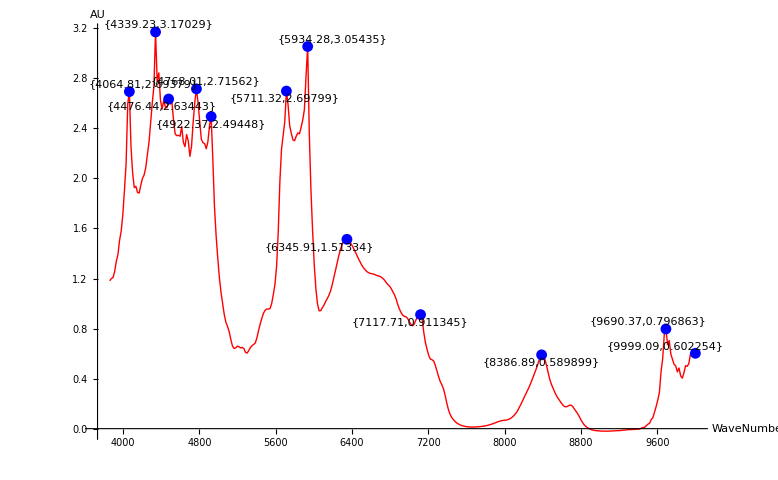

```mathematica
hamamatsu35per = Hamamatsu[1.5,0,0.5]
```

```mathematica
(*WaveNumber Resolution*)
```

```mathematica
(*==============================================================================================*)
(*-----------------------------WaveNumber Resolution 2022-3-19--------------------------------------*)
(*----Utilizing 1550nm laser to disern the broadening of the spectrum line, can refer Raman calibration specs*)
(*==============================================================================================*)
```

```mathematica
HamaFile = SystemDialogInput["FileOpen"]
```

G:\FTIR\near infrared machine examination\2022年03月17日滨松1550nm 激光\第五组\Spectrum.csv

```mathematica
SystemOpen[HamaFile]
HamaResolutionRaw = Import[HamaFile,{"Data",All,1}];
```

```mathematica
effectHamaReso = (NumericQ[#])&/@HamaResolutionRaw;
dropIndexHamaReso = Flatten@Position[effectHamaReso,False];
```

```mathematica
HamaWaveNumber = Drop[HamaResolutionRaw,{1,Max@dropIndexHamaReso}];
```

```mathematica
HamamWavelength = 10^7/HamaWaveNumber;
```

```mathematica
HamaResoValRaw = Import[HamaFile,{"Data",All,2}];
HamaResoVal = Drop[HamaResoValRaw,{1,Max@dropIndexHamaReso}];
HamaResolutionSet = Transpose@Append[{HamamWavelength},HamaResoVal];
```

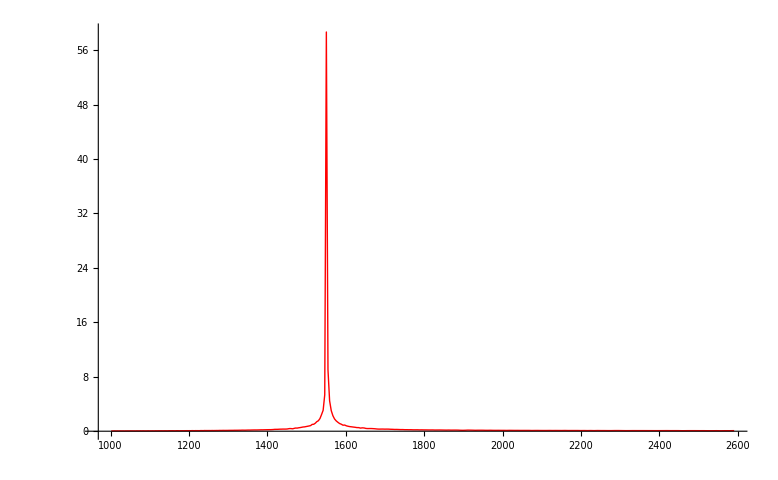

```mathematica
ListPlot[HamaResolutionSet,PlotRange->All,Joined->True,PlotStyle->{Thin,Red}]
```

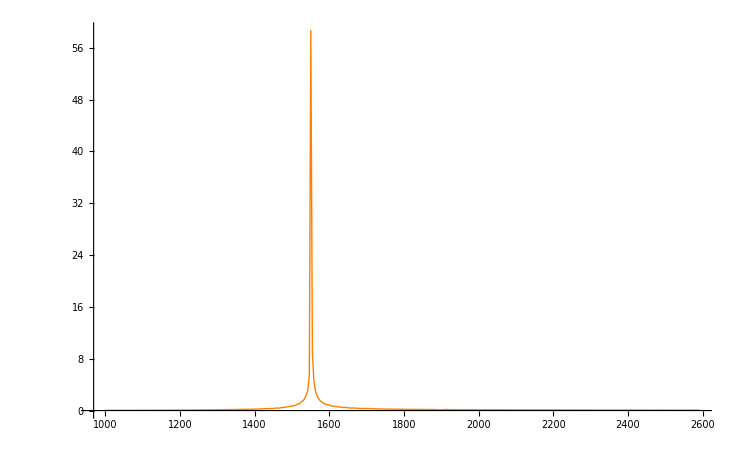

```mathematica
fwhm[func_Function,{min_,max_}]:=Module[{val,maxx,x},{val,maxx}={#1,x/.#2}&@@NMaximize[{func[x],x>min,x<max},x];
Chop@{maxx,Abs[#1-#2]&@@(x/.NSolve[{func[x]==val/2,x>min,x<max},x])}]
```

```mathematica
normHamaResoVal = HamaResoVal/Max[HamaResoVal];
```

```mathematica
L=Length[normHamaResoVal];
```

```mathematica
centerIndex=Position[normHamaResoVal,Max[normHamaResoVal]]⟦1,1⟧
```

152

```mathematica
i=2;
While[Sign[normHamaResoVal[[i]]-0.5]==Sign[normHamaResoVal[[i-1]]-0.5],i=i+1];
Interp=((0.5-normHamaResoVal[[i-1]])/(normHamaResoVal[[i]]-normHamaResoVal[[i-1]]));
Tlead=HamaWaveNumber[[i-1]]+Interp*(HamaWaveNumber[[i]]-HamaWaveNumber[[i-1]])
```

6439.37

```mathematica
Clear[i]
```

```mathematica
i=centerIndex +1;
```

```mathematica
While[Sign[normHamaResoVal[[i]]-0.5]==Sign[normHamaResoVal[[i-1]]-0.5]&&(i≤L-1),i=i+1];
If[i≠L,Interp=(0.5-normHamaResoVal[[i-1]])/(normHamaResoVal[[i]]-normHamaResoVal[[i-1]]);
Ttrail=HamaWaveNumber[[i-1]]+Interp*(HamaWaveNumber[[i]]-HamaWaveNumber[[i-1]]);
FWHM=(Ttrail-Tlead)]
```

19.5758

```mathematica
Ttrail
```

6458.94

```mathematica
HamamatsuReso[]:=Module[{filepath,WNRaw,filterData,dropIndex,waveNumber,wavelength,valRaw,value,normHamaResoVal,L,centerIndex,i,Interp,Tlead,Ttrail,FWHM,ListSet},filepath = SystemDialogInput["FileOpen"];
                                                                       SystemOpen[filepath];
                                                                       WNRaw = Import[filepath,{"Data",All,1}];
                                                                       filterData = (NumericQ[#])&/@WNRaw;
                                                                       dropIndex = Flatten@Position[filterData,False];
                                                                       waveNumber = Drop[WNRaw,{1,Max@dropIndex}];
                                                                       wavelength =Reverse@(10^7/waveNumber);
							       valRaw = Import[filepath,{"Data",All,2}];
                                                                        value = Reverse@Drop[valRaw,{1,Max@dropIndex}];
                                                                        normHamaResoVal = value/Max[value];
							       L=Length[normHamaResoVal];
								centerIndex=Position[normHamaResoVal,Max[normHamaResoVal]]⟦1,1⟧;
							     i=2;
While[Sign[normHamaResoVal[[i]]-0.5]==Sign[normHamaResoVal[[i-1]]-0.5],i=i+1];
Interp=((0.5-normHamaResoVal[[i-1]])/(normHamaResoVal[[i]]-normHamaResoVal[[i-1]]));
Tlead=wavelength[[i-1]]+Interp*(wavelength[[i]]-wavelength[[i-1]]);
Clear[i];
i=centerIndex +1;
While[Sign[normHamaResoVal[[i]]-0.5]==Sign[normHamaResoVal[[i-1]]-0.5]&&(i≤L-1),i=i+1];
If[i≠L,Interp=(0.5-normHamaResoVal[[i-1]])/(normHamaResoVal[[i]]-normHamaResoVal[[i-1]]);
Ttrail=wavelength[[i-1]]+Interp*(wavelength[[i]]-wavelength[[i-1]]);
FWHM=(Ttrail-Tlead)];
 {Tlead,Ttrail,centerIndex,FWHM}
(*ListSet = Transpose[Append[{wavelength},value]];
ListPlot[ListSet,PlotRange->All,Joined->True,PlotStyle->{Thin,Orange}]*)]
```

```mathematica
HamamatsuReso[]
```

{1548.24,1552.95,207,4.70664}

```mathematica
西派特File = SystemDialogInput["FileOpen"]
```

G:\FTIR\near infrared machine examination\2022年03月19日西派特1550nm激光\数据\请 - 03-18 17-50-21-6.txt

```mathematica
SystemOpen[西派特File]
西派特DataSet = Import[西派特File,"Data"];
```

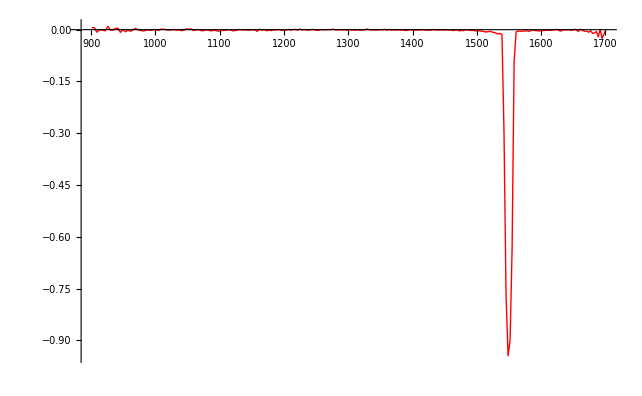

```mathematica
ListPlot[西派特DataSet,PlotRange->All,Joined->True,PlotStyle->{Thin,Red}]
```

```mathematica
西派特SpectrumRaw = 西派特DataSet⟦All,2⟧;
```

```mathematica
西派特wavelength = 西派特DataSet⟦All,1⟧;
```

```mathematica
西派特Spectrum = 西派特SpectrumRaw/Min[西派特SpectrumRaw];
```

```mathematica
L1=Length[西派特Spectrum];
```

```mathematica
西派特centerIndex=Position[西派特Spectrum,Max[西派特Spectrum]]⟦1,1⟧;
```

```mathematica
i=2;
While[Sign[西派特Spectrum[[i]]-0.5]==Sign[西派特Spectrum[[i-1]]-0.5],i=i+1];
Interp=((0.5-西派特Spectrum[[i-1]])/(西派特Spectrum[[i]]-西派特Spectrum[[i-1]]));
Tlead=西派特wavelength[[i-1]]+Interp*(西派特wavelength[[i]]-西派特wavelength[[i-1]])
```

1543.39

```mathematica
Clear[i]
```

```mathematica
i=西派特centerIndex+1;
```

```mathematica
While[Sign[西派特Spectrum[[i]]-0.5]==Sign[西派特Spectrum[[i-1]]-0.5]&&(i≤L1-1),i=i+1];
If[i≠L1,Interp=(0.5-西派特Spectrum[[i-1]])/(西派特Spectrum[[i]]-西派特Spectrum[[i-1]]);
Ttrail=西派特wavelength[[i-1]]+Interp*(西派特wavelength[[i]]-西派特wavelength[[i-1]]);
FWHM=(Ttrail-Tlead)]
```

12.3603